```mathematica
LS=2;
mD[p_]:=4 Sin[1/2(2π p)/LS]^2;
MeanLink[λ_]:=If[λ<4,1-λ/8,2/λ];
m2[λ_]:=λ -2 (1-MeanLink[λ]);
G[λ_,p_]:=1/(m2[λ]+mD[p]);
I0[λ_]:=1/LS Sum[mD[p] G[λ,p],{p,0,LS-1}];
I1[λ_]:=1/LS Sum[mD[p] G[λ,p]^2,{p,0,LS-1}];
S0[λ_]:=1/LS Sum[ G[λ,p],{p,0,LS-1}];
Sunset[λ_,p_]:=1/LS^2 Sum[ G[λ,l1] G[λ,l2] G[λ,p-l1-l2],{l1,0,LS-1},{l2,0,LS-1}];
G0[λ_,p_]:=1/LS G[λ,p];
G1[λ_,p_]:=λ 1/LS G[λ,p]^2 I0[λ];
G2[λ_,p_]:=λ^2(1/LS I0[λ]^2 G[λ,p]^3+1/LS G[λ,p]^2(I0[λ] I1[λ] - m2[λ] S0[λ]^2) +1/LS m2[λ]^2 G[λ,p]^2 Sunset[λ,p]);
GExact[λ_,p_]:=If[λ<4,Which[p==0,1/λ-1/16,p==1,1/16,True,0],Which[p==0,1/(2λ)+1/λ^2,p==1,1/(2λ)-1/λ^2]];
SG[λ_,p_,m_]:=Which[m==0,G0[λ,p],m==1,G0[λ,p]+ G1[λ,p],m==2,G0[λ,p]+ G1[λ,p]+G2[λ,p],True,0];
(*For[p0=0,p0≤1,p0++,
Print[Plot[{GExact[λ,p0],SG[λ,p0,0],SG[λ,p0,1],SG[λ,p0,2]},{λ,0.5,8},PlotStyle->{Black,Blue,Green,Red}]];
];*)
λ0=2.3; 
Print["p = 0: ",N[{G0[λ0,0],G1[λ0,0],G2[λ0,0]}]];
Print["p = 1: ",N[{G0[λ0,1],G1[λ0,1],G2[λ0,1]}]];
```

p = 0: {0.289855,0.135013,0.0275959}

p = 1: {0.0873362,0.0122575,-0.00547291}

```mathematica
FullSimplify[G1[λ,0],{λ<4}]
```

64/(144 λ+27 λ^2)

```mathematica
(* Recursive construction of expansion coefficients *)
LS=2;
mD[p_]:=4 Sin[1/2(2π p)/LS]^2;
(*MeanLink[λ_]:=If[λ<4,1-λ/8,2/λ];*)
MeanLink[λ_]:=2/λ;
m2[λ_]:=λ -2 (1-MeanLink[λ]);
G0[λ_,p_]:=1/(m2[λ]+mD[p]);
DeltaP[p_]:=If[Mod[p,LS]==0,1,0];
(* n is the number of momenta in the correlator *)
(* m is the order in the formal λ - expansion *)
(* P is the 2 n - sized list of momenta *)
G[λ_,P_,m_]:=Module[{n,Res,A,p1t,p2t,q1t,pAt,qAt,m1,m2,P1,P2,i},
n=Length[P]/2;
If[m==0,
(* We're at the bottom of the recursion - just the free propagator *)
Res=Product[1/LS DeltaP[ P[[2 i - 1]]+P[[2 i]] ] G0[λ,P[[2i-1]]] ,{i,1,n}];
,
(* Else - go to lower levels by using the SD equations *)
(* First term in the SD equation *)
Res=If[n>1,1/LS DeltaP[P[[1]]+P[[2]]] G[λ,Drop[P,2],m], 0];
(* Second term in the SD equation - switch momenta *)
For[A=2,A≤n,A++,
P1=Take[P,2(A-1)]; 
P2=Drop[P,2(A-1)];
For[p1t=0,p1t<LS,p1t++,
pAt=P[[1]]+P[[2A-1]]-p1t;
P1[[1]]=p1t; P2[[1]]=pAt;
For[m1=0,m1<m,m1++,
m2=m-m1-1;
Res-=1/LS G[λ,P1,m1] G[λ,P2,m2] ;
];
];
];
(* Third term in SD equations - join sequences with vertex *)
For[A=2,A≤n,A++,
P1=Take[P,2A]; 
P2=Drop[P,2(A-1)];
For[p1t=0,p1t<LS,p1t++,
For[pAt=0,pAt<LS,pAt++,
qAt=P[[1]]-p1t-pAt;
P1[[1]]=p1t;P1[[2A]]=qAt;P2[[1]]=pAt;
For[m1=0,m1<m,m1++,
m2=m-m1-1;
Res+=mD[qAt] G[λ,P1,m1] G[λ,P2,m2] ;
];
];
];
];
(* Fourth term in SD equations - create vertex *)
For[p1t=0,p1t<LS,p1t++,
For[p2t=0,p2t<LS,p2t++,
q1t=P[[1]]-p1t -p2t;
P1=P;
P1[[1]]=p2t;
PrependTo[P1,q1t];
PrependTo[P1,p1t];
Res += mD[q1t] G[λ,P1,m-1];
];
];
(* Final operation *)
Res *= G0[λ,P[[1]]] ;
];
Res
];
GSum=0.0;
ResSummary={};
For[m0=0,m0≤5,m0++,
R=FullSimplify[λ^(m0+1)( G[λ,{0,0},m0]- G[λ,{1,1},m0])];
AppendTo[ResSummary,R];
LR=Limit[R,λ->4];
Print["m0 = ",m0,": ",Expand[R]," => ",LR, "   (",N[LR],")"];
GSum +=N[LR];
];
Print[GSum];
Print[ResSummary]
```

m0 = 0: (2 λ^3)/(16+4 λ^2+λ^4) => 8/21   (0.380952)

m0 = 1: (32 λ^6)/((4+(-2+λ) λ)^2 (4+λ (2+λ))^3)+(8 λ^8)/((4+(-2+λ) λ)^2 (4+λ (2+λ))^3) => 640/3087   (0.207321)

m0 = 2: -(512 λ^8)/((4+(-2+λ) λ)^3 (4+λ (2+λ))^5)+(768 λ^9)/((4+(-2+λ) λ)^3 (4+λ (2+λ))^5)-(512 λ^10)/((4+(-2+λ) λ)^3 (4+λ (2+λ))^5)+(448 λ^11)/((4+(-2+λ) λ)^3 (4+λ (2+λ))^5)-(128 λ^12)/((4+(-2+λ) λ)^3 (4+λ (2+λ))^5)+(48 λ^13)/((4+(-2+λ) λ)^3 (4+λ (2+λ))^5)-(8 λ^14)/((4+(-2+λ) λ)^3 (4+λ (2+λ))^5) => 6656/453789   (0.0146676)

m0 = 3: -(32768 λ^11)/((4+(-2+λ) λ)^4 (4+λ (2+λ))^7)+(30720 λ^12)/((4+(-2+λ) λ)^4 (4+λ (2+λ))^7)-(47104 λ^13)/((4+(-2+λ) λ)^4 (4+λ (2+λ))^7)+(29696 λ^14)/((4+(-2+λ) λ)^4 (4+λ (2+λ))^7)-(19968 λ^15)/((4+(-2+λ) λ)^4 (4+λ (2+λ))^7)+(7424 λ^16)/((4+(-2+λ) λ)^4 (4+λ (2+λ))^7)-(2944 λ^17)/((4+(-2+λ) λ)^4 (4+λ (2+λ))^7)+(480 λ^18)/((4+(-2+λ) λ)^4 (4+λ (2+λ))^7)-(128 λ^19)/((4+(-2+λ) λ)^4 (4+λ (2+λ))^7) => -8855552/66706983   (-0.132753)

m0 = 4: (294912 λ^13)/((4+(-2+λ) λ)^5 (4+λ (2+λ))^9)-(1802240 λ^14)/((4+(-2+λ) λ)^5 (4+λ (2+λ))^9)+(2162688 λ^15)/((4+(-2+λ) λ)^5 (4+λ (2+λ))^9)-(3547136 λ^16)/((4+(-2+λ) λ)^5 (4+λ (2+λ))^9)+(2621440 λ^17)/((4+(-2+λ) λ)^5 (4+λ (2+λ))^9)-(2209792 λ^18)/((4+(-2+λ) λ)^5 (4+λ (2+λ))^9)+(1063936 λ^19)/((4+(-2+λ) λ)^5 (4+λ (2+λ))^9)-(552448 λ^20)/((4+(-2+λ) λ)^5 (4+λ (2+λ))^9)+(163840 λ^21)/((4+(-2+λ) λ)^5 (4+λ (2+λ))^9)-(55424 λ^22)/((4+(-2+λ) λ)^5 (4+λ (2+λ))^9)+(8448 λ^23)/((4+(-2+λ) λ)^5 (4+λ (2+λ))^9)-(1760 λ^24)/((4+(-2+λ) λ)^5 (4+λ (2+λ))^9)+(72 λ^25)/((4+(-2+λ) λ)^5 (4+λ (2+λ))^9) => -1897947136/9805926501   (-0.193551)

m0 = 5: (37224448 λ^16)/((4+(-2+λ) λ)^6 (4+λ (2+λ))^11)-(106168320 λ^17)/((4+(-2+λ) λ)^6 (4+λ (2+λ))^11)+(182583296 λ^18)/((4+(-2+λ) λ)^6 (4+λ (2+λ))^11)-(268894208 λ^19)/((4+(-2+λ) λ)^6 (4+λ (2+λ))^11)+(254410752 λ^20)/((4+(-2+λ) λ)^6 (4+λ (2+λ))^11)-(226295808 λ^21)/((4+(-2+λ) λ)^6 (4+λ (2+λ))^11)+(141426688 λ^22)/((4+(-2+λ) λ)^6 (4+λ (2+λ))^11)-(83103744 λ^23)/((4+(-2+λ) λ)^6 (4+λ (2+λ))^11)+(35356672 λ^24)/((4+(-2+λ) λ)^6 (4+λ (2+λ))^11)-(14143488 λ^25)/((4+(-2+λ) λ)^6 (4+λ (2+λ))^11)+(3975168 λ^26)/((4+(-2+λ) λ)^6 (4+λ (2+λ))^11)-(1050368 λ^27)/((4+(-2+λ) λ)^6 (4+λ (2+λ))^11)+(178304 λ^28)/((4+(-2+λ) λ)^6 (4+λ (2+λ))^11)-(25920 λ^29)/((4+(-2+λ) λ)^6 (4+λ (2+λ))^11)+(2272 λ^30)/((4+(-2+λ) λ)^6 (4+λ (2+λ))^11) => -26053050368/205924456521   (-0.126518)

0.150119

{(2 λ^3)/(16+4 λ^2+λ^4),(8 λ^6 (4+λ^2))/((4+(-2+λ) λ)^2 (4+λ (2+λ))^3),-(8 λ^8 (64+λ (-96+λ (64+λ (-56+λ (16+(-6+λ) λ))))))/((4+(-2+λ) λ)^3 (4+λ (2+λ))^5),-(32 λ^11 (1024+λ (-960+λ (1472+λ (-928+λ (624+λ (-232+λ (92+λ (-15+4 λ)))))))))/((4+(-2+λ) λ)^4 (4+λ (2+λ))^7),(8 λ^13 (36864+λ (-225280+λ (270336+λ (-443392+λ (327680+λ (-276224+λ (132992+λ (-69056+λ (20480+λ (-6928+λ (1056+λ (-220+9 λ)))))))))))))/((4+(-2+λ) λ)^5 (4+λ (2+λ))^9),1/((4+(-2+λ) λ)^6 (4+λ (2+λ))^11)32 λ^16 (1163264+λ (-3317760+λ (5705728+λ (-8402944+λ (7950336+λ (-7071744+λ (4419584+λ (-2596992+λ (1104896+λ (-441984+λ (124224+λ (-32824+λ (5572+λ (-810+71 λ))))))))))))))}

```mathematica
(* Here we collect analytic expressions for different m *)
```

```mathematica
UoWC[λ_]:={32/(48+9 λ)+(12 λ)/(48+9 λ),
16384/(9 (16+3 λ)^3)+(2048 λ)/(3 (16+3 λ)^3)+(128 λ^2)/(16+3 λ)^3,
8388608/(27 (16+3 λ)^5)+(1048576 λ)/(9 (16+3 λ)^5)-(65536 λ^2)/(3 (16+3 λ)^5)-(8192 λ^3)/(16+3 λ)^5-(1536 λ^4)/(16+3 λ)^5,
4294967296/(81 (16+3 λ)^7)-(268435456 λ)/(27 (16+3 λ)^7)-(385875968 λ^2)/(9 (16+3 λ)^7)-(20971520 λ^3)/(16+3 λ)^7-(3538944 λ^4)/(16+3 λ)^7-(344064 λ^5)/(16+3 λ)^7,
2199023255552/(243 (16+3 λ)^9)-(1786706395136 λ)/(81 (16+3 λ)^9)-(300647710720 λ^2)/(9 (16+3 λ)^9)-(156766306304 λ^3)/(9 (16+3 λ)^9)-(13321109504 λ^4)/(3 (16+3 λ)^9)-(452984832 λ^5)/(16+3 λ)^9-(22020096 λ^6)/(16+3 λ)^9+(2359296 λ^7)/(16+3 λ)^9,
1125899906842624/(729 (16+3 λ)^11)-(3659174697238528 λ)/(243 (16+3 λ)^11)-(1697645953286144 λ^2)/(81 (16+3 λ)^11)-(300441552289792 λ^3)/(27 (16+3 λ)^11)-(2834678415360 λ^4)/(16+3 λ)^11-(261993005056 λ^5)/(16+3 λ)^11+(50465865728 λ^6)/(16+3 λ)^11+(10569646080 λ^7)/(16+3 λ)^11+(1132462080 λ^8)/(16+3 λ)^11
};
LoWC[λ_]:={32/(48+9 λ),
16384/(9 (16+3 λ)^3)+(2048 λ)/(3 (16+3 λ)^3),
8388608/(27 (16+3 λ)^5)+(1048576 λ)/(9 (16+3 λ)^5)-(8192 λ^3)/(16+3 λ)^5,
4294967296/(81 (16+3 λ)^7)-(268435456 λ)/(27 (16+3 λ)^7)-(285212672 λ^2)/(9 (16+3 λ)^7)-(35651584 λ^3)/(3 (16+3 λ)^7)-(2097152 λ^4)/(16+3 λ)^7,
2199023255552/(243 (16+3 λ)^9)-(1786706395136 λ)/(81 (16+3 λ)^9)-(249108103168 λ^2)/(9 (16+3 λ)^9)-(11811160064 λ^3)/(16+3 λ)^9-(6878658560 λ^4)/(3 (16+3 λ)^9)-(234881024 λ^5)/(16+3 λ)^9+(14155776 λ^6)/(16+3 λ)^9,
1125899906842624/(729 (16+3 λ)^11)-(3659174697238528 λ)/(243 (16+3 λ)^11)-(1460151441686528 λ^2)/(81 (16+3 λ)^11)-(71193377898496 λ^3)/(9 (16+3 λ)^11)-(1494648619008 λ^4)/(16+3 λ)^11-(92341796864 λ^5)/(3 (16+3 λ)^11)+(24696061952 λ^6)/(16+3 λ)^11+(7147094016 λ^7)/(16+3 λ)^11
};
UoSC[λ_]:={(λ^2 (4+λ^2))/(16+4 λ^2+λ^4),(2 λ^5 (16+12 λ^2+λ^4))/((4+(-2+λ) λ)^2 (4+λ (2+λ))^3),-(2 λ^7 (256+λ (4+λ^2) (-64+(-2+λ) λ (-48+λ (16+(-2+λ) λ)))))/((4+(-2+λ) λ)^3 (4+λ (2+λ))^5),-(4 λ^10 (7168+λ (-4096+λ (14592+λ (-9472+λ (9920+λ (-4416+λ (2480+λ (-592+λ (228+λ (-16+7 λ)))))))))))/((4+(-2+λ) λ)^4 (4+λ (2+λ))^7),(16 λ^12 (16384+λ (-86016+λ (90112+λ (-235008+λ (186368+λ (-220416+λ (122624+λ (-84256+λ (30656+λ (-13776+λ (2912+λ (-918+λ (88+(-21+λ) λ))))))))))))))/((4+(-2+λ) λ)^5 (4+λ (2+λ))^9),1/((4+(-2+λ) λ)^6 (4+λ (2+λ))^11)32 λ^15 (983040+λ (-2211840+λ (4366336+λ (-7839744+λ (8577024+λ (-9575424+λ (6990848+λ (-5078272+λ (2560768+λ (-1269568+λ (436928+λ (-149616+λ (33504+λ (-7656+λ (1066+15 (-9+λ) λ)))))))))))))))};
LoSC[λ_]:={(2 λ^3)/(16+4 λ^2+λ^4),(8 λ^6 (4+λ^2))/((4+(-2+λ) λ)^2 (4+λ (2+λ))^3),-(8 λ^8 (64+λ (-96+λ (64+λ (-56+λ (16+(-6+λ) λ))))))/((4+(-2+λ) λ)^3 (4+λ (2+λ))^5),-(32 λ^11 (1024+λ (-960+λ (1472+λ (-928+λ (624+λ (-232+λ (92+λ (-15+4 λ)))))))))/((4+(-2+λ) λ)^4 (4+λ (2+λ))^7),(8 λ^13 (36864+λ (-225280+λ (270336+λ (-443392+λ (327680+λ (-276224+λ (132992+λ (-69056+λ (20480+λ (-6928+λ (1056+λ (-220+9 λ)))))))))))))/((4+(-2+λ) λ)^5 (4+λ (2+λ))^9),1/((4+(-2+λ) λ)^6 (4+λ (2+λ))^11)32 λ^16 (1163264+λ (-3317760+λ (5705728+λ (-8402944+λ (7950336+λ (-7071744+λ (4419584+λ (-2596992+λ (1104896+λ (-441984+λ (124224+λ (-32824+λ (5572+λ (-810+71 λ))))))))))))))};

U[λ_,m_]:=Module[{mUo,i},
mUo=If[λ<4,UoWC[λ],UoSC[λ]];
Sum[mUo[[i]],{i,1,m+1}]
];
L[λ_,m_]:=Module[{mLo,i},
mLo=If[λ<4,LoWC[λ],LoSC[λ]];
Sum[mLo[[i]],{i,1,m+1}]
];
```

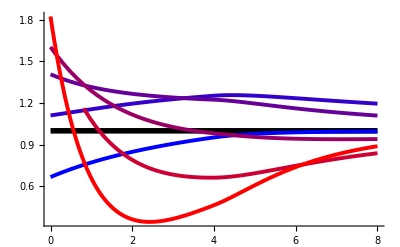

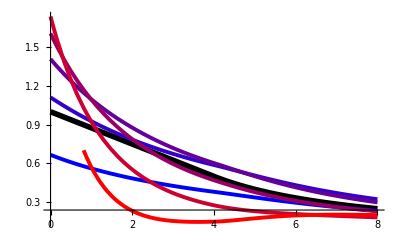

```mathematica
GrU={Plot[1,{λ,0,8},PlotStyle->{Thickness[0.01],Black}]};
GrL={Plot[If[λ<4,1-λ/8,2/λ],{λ,0,8},PlotStyle->{Thickness[0.01],Black}]};
For[m0=0,m0≤5,m0++,
r=m0/5;
AppendTo[GrU,Plot[U[λ,m0],{λ,0,8},PlotStyle->{Thickness[0.007],RGBColor[r,0,1-r]}]];AppendTo[GrL,Plot[L[λ,m0],{λ,0,8},PlotStyle->{Thickness[0.007],RGBColor[r,0,1-r]}]];
];
Show[GrU,PlotRange->All]
Show[GrL,PlotRange->All]
```